# ConvexificationDynamics

## Quantitative mode dominance and convergence to the pair-plane

## Purpose

This notebook isolates the dynamical part of Chapter 2. It studies repeated application of the averaging operator A_α, decomposes polygon data into the first-harmonic pair-plane E_(±1) and its higher-mode complement, and compares the observed decay of higher modes with the spectral estimate.

All executable cells are ordinary Wolfram Language input. Typeset boxes are used only in explanatory text.

## 1. Definitions

```mathematica
ClearAll["Global`*"];

omega[n_Integer?Positive] := Exp[2 Pi I/n];

fourierVector[n_Integer?Positive, k_Integer] :=
  Table[omega[n]^(j k), {j, 0, n - 1}]/Sqrt[n];

fourierMatrix[n_Integer?Positive] :=
  Transpose@Table[fourierVector[n, k], {k, 0, n - 1}];

averagingMatrix[n_Integer?Positive, alpha_?NumericQ] :=
  Table[
    (1 - alpha) Boole[ell == j] + alpha Boole[ell == Mod[j + 1, n]],
    {j, 0, n - 1}, {ell, 0, n - 1}
  ];

applyA[p_List, alpha_?NumericQ] :=
  (1 - alpha) p + alpha RotateLeft[p];

lambda[n_Integer?Positive, k_Integer, alpha_] :=
  (1 - alpha) + alpha Exp[2 Pi I k/n];

mu[n_Integer?Positive, k_Integer, alpha_] :=
  Abs[lambda[n, k, alpha]];
```

The operator is

(A_α p)_j=(1-α)p_j+α p_(j+1)

```mathematica
nExample = 12;
alphaExample = 0.35;
A = averagingMatrix[nExample, alphaExample];
```

## 2. Fourier diagonalization

The Fourier eigenvalues are

λ_k=(1-α)+α e^((2πik)/n)

```mathematica
F = fourierMatrix[nExample];
lambdaList = Table[lambda[nExample, k, alphaExample], {k, 0, nExample - 1}];
diagonalizedA = Chop[ConjugateTranspose[F] . A . F];
diagonalizationError = Max[Abs[Flatten[N[diagonalizedA - DiagonalMatrix[lambdaList]]]]];
diagonalizationQ = diagonalizationError < 10^-10;
```

```mathematica
diagonalizationError
```

3.43318×10^-16

```mathematica
diagonalizationQ
```

True

## 3. Fourier decomposition of polygon data

```mathematica
fourierCoefficients[p_List] := Module[{F = fourierMatrix[Length[p]]},
  ConjugateTranspose[F] . p
];

reconstructFromCoefficients[c_List] := Module[{F = fourierMatrix[Length[c]]},
  F . c
];

centerPolygon[p_List] := p - Mean[p];

pairPlaneCoefficients[p_List] := Module[{n = Length[p], c = fourierCoefficients[p], result},
  result = ConstantArray[0, n];
  result[[2]] = c[[2]];
  result[[n]] = c[[n]];
  result
];

higherModeCoefficients[p_List] := Module[{n = Length[p], c = fourierCoefficients[p], result},
  result = c;
  result[[1]] = 0;
  result[[2]] = 0;
  result[[n]] = 0;
  result
];

pairPlaneProjection[p_List] :=
  reconstructFromCoefficients[pairPlaneCoefficients[p]];

higherModeProjection[p_List] :=
  reconstructFromCoefficients[higherModeCoefficients[p]];
```

```mathematica
SeedRandom[2026];
pExample = RandomReal[{-1, 1}, nExample] + I RandomReal[{-1, 1}, nExample];
pExample = centerPolygon[pExample];

xExample = pairPlaneProjection[pExample];
yExample = higherModeProjection[pExample];
decompositionError = Norm[pExample - xExample - yExample];
decompositionQ = decompositionError < 10^-10;
```

```mathematica
decompositionError
```

1.00468×10^-15

```mathematica
decompositionQ
```

True

## 4. Iteration in physical and Fourier coordinates

```mathematica
iteratePhysical[p_List, alpha_?NumericQ, m_Integer?NonNegative] :=
  Nest[applyA[#, alpha] &, N[p], m];

iterateFourier[p_List, alpha_?NumericQ, m_Integer?NonNegative] := Module[
  {n = Length[p], c, factors},
  c = fourierCoefficients[p];
  factors = Table[lambda[n, k, alpha]^m, {k, 0, n - 1}];
  reconstructFromCoefficients[factors c]
];
```

```mathematica
iterationAgreementError = Max@Table[
  Norm[iteratePhysical[pExample, alphaExample, m] - iterateFourier[pExample, alphaExample, m]],
  {m, 0, 30}
];
iterationAgreementQ = iterationAgreementError < 10^-9;
```

```mathematica
iterationAgreementError
```

1.03369×10^-15

```mathematica
iterationAgreementQ
```

True

## 5. Quantitative mode dominance

Write p=x+y with x∈E_(±1) and y∈(E_(±1))^⊥. The relevant decay factor is

ρ=μ_2/μ_1<1

```mathematica
modeNorms[p_List] := Module[{c = fourierCoefficients[p], n = Length[p]},
  <|
    "PairPlane" -> Sqrt[Abs[c[[2]]]^2 + Abs[c[[n]]]^2],
    "HigherModes" -> Sqrt[Total[Abs[c[[3 ;; n - 1]]]^2]]
  |>
];

modeConstant[p_List] := Module[{norms = modeNorms[p]},
  norms["HigherModes"]/norms["PairPlane"]
];

spectralRatio[n_Integer?Positive, alpha_?NumericQ] :=
  mu[n, 2, alpha]/mu[n, 1, alpha];

dominanceRatio[p_List, alpha_?NumericQ, m_Integer?NonNegative] := Module[
  {iterate, pairNorm, higherNorm},
  iterate = iterateFourier[p, alpha, m];
  pairNorm = Norm[pairPlaneProjection[iterate]];
  higherNorm = Norm[higherModeProjection[iterate]];
  higherNorm/pairNorm
];

dominanceBound[p_List, alpha_?NumericQ, m_Integer?NonNegative] :=
  modeConstant[p] spectralRatio[Length[p], alpha]^m;
```

```mathematica
rhoExample = spectralRatio[nExample, alphaExample];
CExample = modeConstant[pExample];
{rhoExample, CExample}
```

{0.906999,7.29361}

```mathematica
dominanceTable = Table[
  {
    m,
    dominanceRatio[pExample, alphaExample, m],
    dominanceBound[pExample, alphaExample, m]
  },
  {m, 0, 50, 5}
];
dominanceTable // TableForm
```

0 | 7.29361 | 7.29361
5 | 2.00687 | 4.47689
10 | 1.09583 | 2.74796
15 | 0.657389 | 1.68673
20 | 0.401857 | 1.03533
25 | 0.246486 | 0.635497
30 | 0.151277 | 0.390075
35 | 0.0928532 | 0.239432
40 | 0.056994 | 0.146966
45 | 0.0349835 | 0.0902091
50 | 0.0214732 | 0.0553713

```mathematica
dominanceResiduals = Table[
  dominanceRatio[pExample, alphaExample, m] - dominanceBound[pExample, alphaExample, m],
  {m, 0, 50}
];
maxDominanceResidual = Max[dominanceResiduals];
dominanceQ = maxDominanceResidual < 10^-9;
```

```mathematica
maxDominanceResidual
```

0.

```mathematica
dominanceQ
```

True

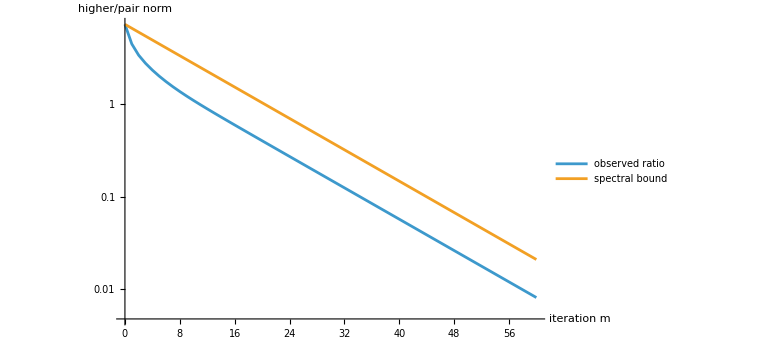

```mathematica
ListLogPlot[
  {
    Table[{m, dominanceRatio[pExample, alphaExample, m]}, {m, 0, 60}],
    Table[{m, dominanceBound[pExample, alphaExample, m]}, {m, 0, 60}]
  },
  Joined -> True,
  PlotLegends -> {"observed ratio", "spectral bound"},
  AxesLabel -> {"iteration m", "higher/pair norm"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 6. Directional convergence to the pair-plane

After normalization by the size of the first-harmonic component, the higher-mode contribution tends to zero.

```mathematica
pairNormalizedIterate[p_List, alpha_?NumericQ, m_Integer?NonNegative] := Module[
  {iterate, scale},
  iterate = iterateFourier[p, alpha, m];
  scale = Norm[pairPlaneProjection[iterate]];
  iterate/scale
];

pairNormalizedLimit[p_List] := Module[{x = pairPlaneProjection[p]},
  x/Norm[x]
];

directionalError[p_List, alpha_?NumericQ, m_Integer?NonNegative] := Module[
  {normalized, pairPart},
  normalized = pairNormalizedIterate[p, alpha, m];
  pairPart = pairPlaneProjection[normalized];
  Norm[normalized - pairPart]
];
```

```mathematica
directionalTable = Table[
  {m, directionalError[pExample, alphaExample, m]},
  {m, 0, 60, 5}
];
directionalTable // TableForm
```

0 | 7.29361
5 | 2.00687
10 | 1.09583
15 | 0.657389
20 | 0.401857
25 | 0.246486
30 | 0.151277
35 | 0.0928532
40 | 0.056994
45 | 0.0349835
50 | 0.0214732
55 | 0.0131805
60 | 0.00809032

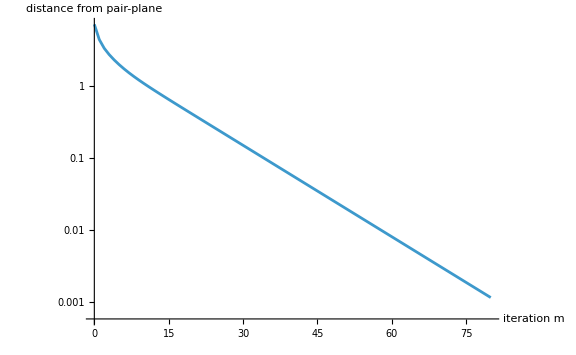

```mathematica
ListLogPlot[
  Table[{m, directionalError[pExample, alphaExample, m]}, {m, 0, 80}],
  Joined -> True,
  AxesLabel -> {"iteration m", "distance from pair-plane"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 7. Empirical decay rate

The logarithm of the dominance ratio should be approximately affine in m, with slope logρ.

```mathematica
fitRange = Range[5, 50];
fitData = Table[
  {m, Log[dominanceRatio[pExample, alphaExample, m]]},
  {m, fitRange}
];
linearFit = LinearModelFit[fitData, m, m];
empiricalSlope = linearFit["BestFitParameters"][[2]];
theoreticalSlope = Log[rhoExample];
slopeError = Abs[empiricalSlope - theoreticalSlope];
```

```mathematica
{empiricalSlope, theoreticalSlope, slopeError}
```

{-0.0988873,-0.0976139,0.00127345}

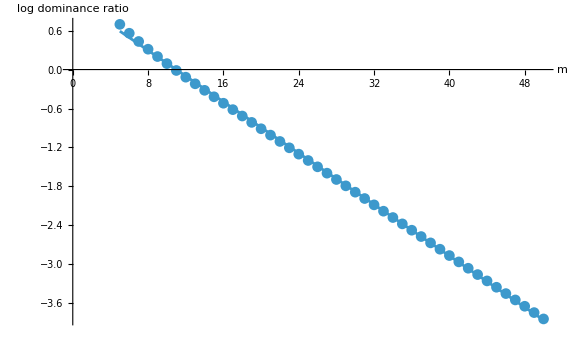

```mathematica
Show[
  ListPlot[fitData, PlotMarkers -> Automatic],
  Plot[linearFit[m], {m, Min[fitRange], Max[fitRange]}],
  AxesLabel -> {"m", "log dominance ratio"},
  ImageSize -> Large
]
```

## 8. Polygon visualization

```mathematica
Clear[polygonPoints, polygonPlot];

polygonPoints[p_List] := N@Transpose[{Re[p], Im[p]}];

polygonPlot[p_List, title_: None] := Module[{pts},
  pts = polygonPoints[p];
  Graphics[
    {
      Thick,
      Line[Append[pts, First[pts]]],
      PointSize[0.018],
      Point[pts]
    },
    Axes -> True,
    AspectRatio -> 1,
    PlotRange -> All,
    PlotLabel -> title,
    ImageSize -> Large
  ]
];
```

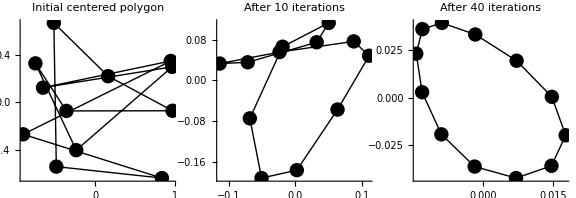

```mathematica
GraphicsRow[
  {
    polygonPlot[pExample, "Initial centered polygon"],
    polygonPlot[iteratePhysical[pExample, alphaExample, 10], "After 10 iterations"],
    polygonPlot[iteratePhysical[pExample, alphaExample, 40], "After 40 iterations"]
  },
  ImageSize -> Large
]
```

## 9. Shape-normalized animation

Raw iterates shrink. For visualization, each iterate is centered and divided by the norm of its pair-plane component.

```mathematica
shapeNormalizedIterate[p_List, alpha_?NumericQ, m_Integer?NonNegative] := Module[
  {iterate, centered, scale},
  iterate = iteratePhysical[p, alpha, m];
  centered = centerPolygon[iterate];
  scale = Norm[pairPlaneProjection[centered]];
  centered/scale
];
```

```mathematica
shapeNormalizedFrame[m_Integer?NonNegative] :=
  polygonPlot[
    shapeNormalizedIterate[pExample, alphaExample, m],
    Row[{"Shape-normalized iterate, m = ", m}]
  ];
```

```mathematica
{
  Head[Row[{"Shape-normalized iterate, m = ", 0}]],
  MatchQ[Row[{"Shape-normalized iterate, m = ", 0}], _String],
  MatchQ[Row[{"Shape-normalized iterate, m = ", 0}], _]
}
```

{Row,False,True}

```mathematica
Head[polygonPlot[{0, 1, I}, "Polygon plot diagnostic"]]
```

Graphics

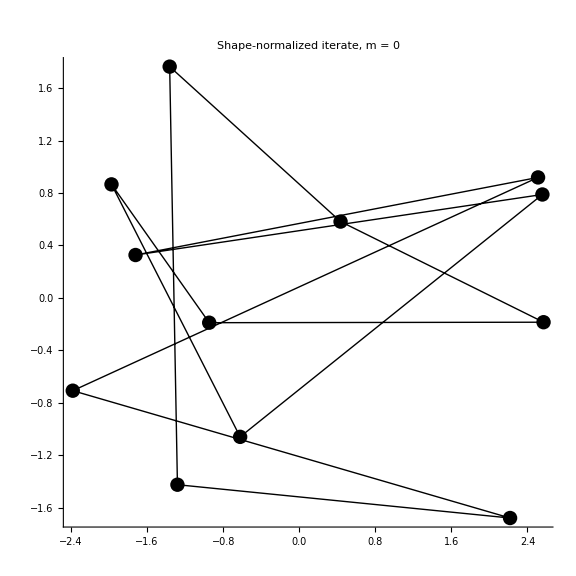

```mathematica
shapeNormalizedFrame[0]
```

```mathematica
animationFrames = Table[shapeNormalizedFrame[m], {m, 0, 80}];
```

```mathematica
ListAnimate[animationFrames, DefaultDuration -> 12]
```

The first cell above always produces a static plot. The animation is then built from precomputed graphics using ListAnimate, avoiding reliance on a held Manipulate expression.

## 10. Mode-amplitude evolution

```mathematica
modeAmplitudeTable[p_List, alpha_?NumericQ, maxM_Integer?NonNegative] := Module[
  {n = Length[p], c = fourierCoefficients[p]},
  Table[
    Prepend[
      Table[Abs[c[[k + 1]] lambda[n, k, alpha]^m], {k, 1, n - 1}],
      m
    ],
    {m, 0, maxM}
  ]
];

amplitudeData = modeAmplitudeTable[pExample, alphaExample, 50];
```

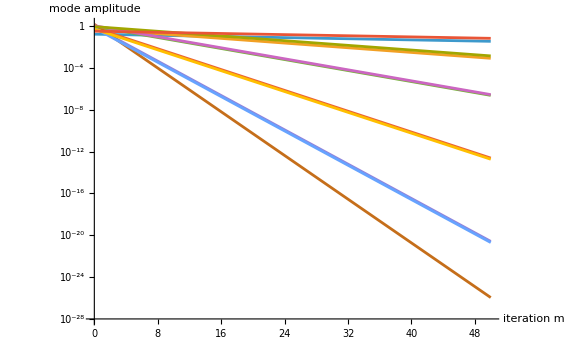

```mathematica
ListLogPlot[
  Table[
    Table[{row[[1]], row[[k + 1]]}, {row, amplitudeData}],
    {k, 1, nExample - 1}
  ],
  Joined -> True,
  AxesLabel -> {"iteration m", "mode amplitude"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 11. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[24];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[
      {alpha = 0.37, p, F, A, lambdas, diagError, decompError, iterError, rho},
      SeedRandom[1000 + n];
      p = RandomReal[{-1, 1}, n] + I RandomReal[{-1, 1}, n];
      p = centerPolygon[p];
      F = fourierMatrix[n];
      A = averagingMatrix[n, alpha];
      lambdas = Table[lambda[n, k, alpha], {k, 0, n - 1}];
      diagError = Max[Abs[Flatten[N[
        ConjugateTranspose[F] . A . F - DiagonalMatrix[lambdas]
      ]]]];
      decompError = Norm[N[p - pairPlaneProjection[p] - higherModeProjection[p]]];
      iterError = Max@Table[
        Norm[N[iteratePhysical[p, alpha, m] - iterateFourier[p, alpha, m]]],
        {m, 0, 12}
      ];
      rho = spectralRatio[n, alpha];
      <|
        "n" -> n,
        "Fourier diagonalization" -> TrueQ[diagError < 10^-9],
        "Orthogonal decomposition" -> TrueQ[decompError < 10^-9],
        "Physical/Fourier iteration" -> TrueQ[iterError < 10^-8],
        "Spectral ratio below one" -> TrueQ[rho < 1]
      |>
    ],
    {n, 5, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
Length[DownValues[verificationReport]]
```

2

```mathematica
verificationReport[]
```

## Conclusion

The computations exhibit the mechanism behind convexification dynamics: the first-harmonic pair E_(±1) decays more slowly than all higher Fourier modes, so the relative higher-mode contribution decreases geometrically at a rate controlled by μ_2/μ_1. The shape-normalized iterates therefore approach the pair-plane.